Part 2 of the Assignment

this is a plot of the difference between the series and sin(x) as a function of x

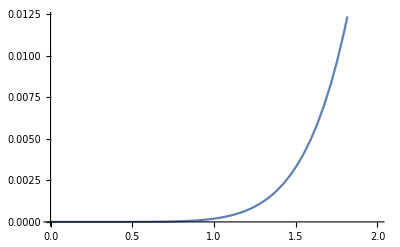

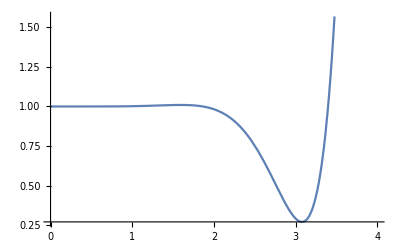

This plot show that SerCos[x,n]^2+SerSin[x,n]^2 is nearly 1 around 0, but is not constant when the taylor approximation becomes less reliable (farther from 0).

(x^6 (40-15 x^2+x^4))/14400

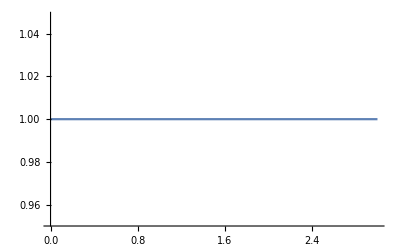

The graph is constant at 1, as expected

```mathematica
TextCell["Part 2 of the Assignment"]
SerCos[x_,n_]:=Normal[Series[Cos[y],{y,0,n}]]/.y->x
SerSin[x_,n_]:=Normal[Series[Sin[y],{y,0,n}]]/.y->x
TextCell["this is a plot of the difference between the series and sin(x) as a function of x"]
Plot[SerSin[x,5]-Sin[x],{x,0,2}]
Plot[SerSin[x,5]^2 + SerCos[x,5]^2, {x,0,4}]
TextCell["This plot show that SerCos[x,n]^2+SerSin[x,n]^2 is nearly 1 around 0, but is not constant when the taylor approximation becomes less reliable (farther from 0). " ]
Simplify[(SerSin[x,5]^2+SerCos[x,5]^2)-1]
TextCell[
"Algebraically we can see this is true as well. As x increases, the numerator grows, and the difference between the taylor approximation and 1 becomes non negligible"] 
SerCosSq[x_,n_]:=Normal[Series[Cos[y]^2,{y,0,n}]]/.y->x
SerSinSq[x_,n_]:=Normal[Series[Sin[y]^2,{y,0,n}]]/.y->x
Plot[SerCosSq[x,5]+SerSinSq[x,5],{x,0,3}]
TextCell["The graph is constant at 1, as expected"]
```

```mathematica
TextCell["Part 3 of the Assignment"]
Rx[θ_]:={{1,0,0},{0,Cos[θ],-Sin[θ]},{0,Sin[θ],Cos[θ]}}
Ry[ζ_]:={{Cos[ζ],0,Sin[ζ]},{0,1,0},{-Sin[ζ],0,Cos[ζ]}}
Rz[ϕ_]:={{Cos[ϕ],-Sin[ϕ],0},{Sin[ϕ],Cos[ϕ],0},{0,0,1}}
Rot3[ψ,θ,ϕ]:= Rz[ψ].Rx[θ].Rz[ϕ]
MatrixForm[Rx[θ]]
MatrixForm[Ry[ζ]]
MatrixForm[Rz[ϕ]]
MatrixForm[Simplify[Rot3[ψ,θ,ϕ]]]
TextCell["The general rotation matrix does not simplify"]
Rot3Inverse[ψ,θ,ϕ]:=FullSimplify[Rz[-ϕ].Rx[-θ].Rz[-ψ]]
Simplify[Rot3Inverse[ψ,θ,ϕ].Rot3[ψ,θ,ϕ]]
TextCell["this is the identity matrix as expected"]
Simplify[Inverse[Rot3[ψ,θ,ϕ]].Rot3[ψ,θ,ϕ]]
Simplify[Rot3Inverse[ψ,θ,ϕ]-Inverse[Rot3[ψ,θ,ϕ]]]
```

Part 3 of the Assignment

(1 | 0 | 0
0 | Cos[θ] | -Sin[θ]
0 | Sin[θ] | Cos[θ])

(Cos[ζ] | 0 | Sin[ζ]
0 | 1 | 0
-Sin[ζ] | 0 | Cos[ζ])

(Cos[ϕ] | -Sin[ϕ] | 0
Sin[ϕ] | Cos[ϕ] | 0
0 | 0 | 1)

(Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ] | -Cos[ψ] Sin[ϕ]-Cos[θ] Cos[ϕ] Sin[ψ] | Sin[θ] Sin[ψ]
Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ] | Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ] | -Cos[ψ] Sin[θ]
Sin[θ] Sin[ϕ] | Cos[ϕ] Sin[θ] | Cos[θ])

The general rotation matrix does not simplify

{{1,0,0},{0,1,0},{0,0,1}}

{{1,0,0},{0,1,0},{0,0,1}}

{{0,0,0},{0,0,0},{0,0,0}}